### Start choosing the example:

```mathematica
t=31;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5},Adjacency Matrix→{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{5,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3,4,5},Adjacency Matrix→{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{5,U1}},Switching Costs→{}|>

```mathematica
Keys@MFGEquations
```

{BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,FVL,AllTransitions,NoDeadEnds,NoDeadStarts,jargs,js,jvars,jts,jtvars,uargs,us,uvars,SwitchingCosts,OutRules,InRules,EntryArgs,EntryDataAssociation,jays,NonZeroEntryCurrents,ExitCosts,EqCurrentCompCon,EqTransitionCompCon,EqCompCon,EqAllComp,EqPosCon,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EqEntryIn,EqExitValues,EqSwitchingConditions,EqValueAuxiliaryEdges,EqAll,EqAllCompRules,EqAllRules,EqAllAll,BoundaryRules,reduced1,reduced2,EqAllAllSimple,RulesEntryIn,RulesExitValues,EqAllAllRules,Nlhs,EqCriticalCase,criticalreduced1,criticalreduced2,Nrhs,EqGeneralCase,TOL}

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2, U1-> 0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.013066,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→8,u122→6,u123→4,u124→2,u125→0,u126→8,u127→-2+8,u128→-2+6,u129→-2+4,u130→-2+2,u131→0,u132→8|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→4.18612,u122→3.13959,u123→2.09306,u124→1.04653,u125→0,u126→4.18612,u127→3.13959,u128→2.09306,u129→1.04653,u130→0,u131→0,u132→4.18612|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.44089×10^-16

FRX1: The Error on the nonlinear terms is 4.44089×10^-16

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→4.39627,u122→3.2972,u123→2.19814,u124→1.09907,u125→0,u126→4.39627,u127→3.2972,u128→2.19814,u129→1.09907,u130→0,u131→0,u132→4.39627|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→4.88643,u122→3.66483,u123→2.44322,u124→1.22161,u125→0,u126→4.88643,u127→3.66483,u128→2.44322,u129→1.22161,u130→0,u131→0,u132→4.88643|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→7.33396,u122→5.50047,u123→3.66698,u124→1.83349,u125→0,u126→7.33396,u127→5.50047,u128→3.66698,u129→1.83349,u130→0,u131→0,u132→7.33396|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.44089×10^-15

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→8,u122→6,u123→4,u124→2,u125→0,u126→8,u127→6,u128→4,u129→2,u130→0,u131→0,u132→8|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→9.77058,u122→7.32794,u123→4.88529,u124→2.44265,u125→0,u126→9.77058,u127→7.32794,u128→4.88529,u129→2.44265,u130→0,u131→0,u132→9.77058|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→14.5709,u122→10.9282,u123→7.28546,u124→3.64273,u125→0,u126→14.5709,u127→10.9282,u128→7.28546,u129→3.64273,u130→0,u131→0,u132→14.5709|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→17.3829,u122→13.0372,u123→8.69147,u124→4.34573,u125→0,u126→17.3829,u127→13.0372,u128→8.69147,u129→4.34573,u130→0,u131→0,u132→17.3829|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→17.3863,u122→13.0397,u123→8.69314,u124→4.34657,u125→0,u126→17.3863,u127→13.0397,u128→8.69314,u129→4.34657,u130→0,u131→0,u132→17.3863|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.10543×10^-15

FRX1: The Error on the nonlinear terms is 7.10543×10^-15

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→65.4928,u122→49.1196,u123→32.7464,u124→16.3732,u125→0,u126→65.4928,u127→49.1196,u128→32.7464,u129→16.3732,u130→0,u131→0,u132→65.4928|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→17.5514,u122→13.1636,u123→8.77571,u124→4.38786,u125→0,u126→17.5514,u127→13.1636,u128→8.77571,u129→4.38786,u130→0,u131→0,u132→17.5514|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→17.7231,u122→13.2923,u123→8.86156,u124→4.43078,u125→0,u126→17.7231,u127→13.2923,u128→8.86156,u129→4.43078,u130→0,u131→0,u132→17.7231|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→18.0765,u122→13.5573,u123→9.03823,u124→4.51911,u125→0,u126→18.0765,u127→13.5573,u128→9.03823,u129→4.51911,u130→0,u131→0,u132→18.0765|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→19.2234,u122→14.4175,u123→9.61169,u124→4.80584,u125→0,u126→19.2234,u127→14.4175,u128→9.61169,u129→4.80584,u130→0,u131→0,u132→19.2234|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→21.4823,u122→16.1117,u123→10.7411,u124→5.37057,u125→0,u126→21.4823,u127→16.1117,u128→10.7411,u129→5.37057,u130→0,u131→0,u132→21.4823|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→27.9637,u122→20.9727,u123→13.9818,u124→6.99091,u125→0,u126→27.9637,u127→20.9727,u128→13.9818,u129→6.99091,u130→0,u131→0,u132→27.9637|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→39.5765,u122→29.6824,u123→19.7883,u124→9.89413,u125→0,u126→39.5765,u127→29.6824,u128→19.7883,u129→9.89413,u130→0,u131→0,u132→39.5765|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.10543×10^-15

FRX1: The Error on the nonlinear terms is 7.10543×10^-15

<|j100→2,j101→2,j102→2,j103→2,j104→2,j105→0,j106→0,j107→0,j108→0,j109→0,j110→0,j99→2,jt111→0,jt112→2,jt113→2,jt114→0,jt115→2,jt116→0,jt117→2,jt118→0,jt119→2,jt120→0,u121→65.4928,u122→49.1196,u123→32.7464,u124→16.3732,u125→0,u126→65.4928,u127→49.1196,u128→32.7464,u129→16.3732,u130→0,u131→0,u132→65.4928|>

### What we this plot for?

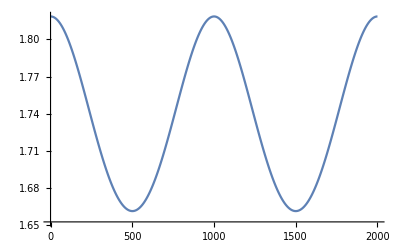

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.